0.600535

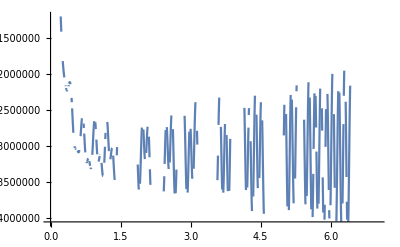

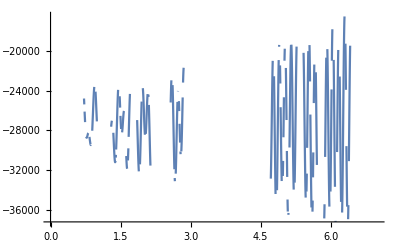

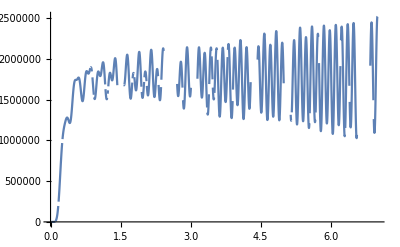

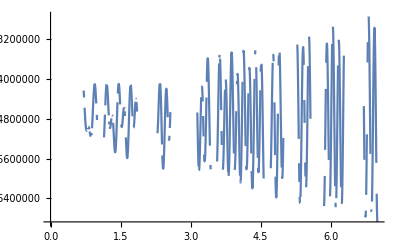

Thread::tdlen: Objects of unequal length in {«1»} {1} cannot be combined.

Thread::tdlen: Objects of unequal length in (:ff1b)^2 cannot be combined.

Thread::tdlen: Objects of unequal length in ；^2 «2» {{(-3.96999×10^7+3.66526×10^9 s+«6»+248.079 s^8+9.80665 s^9)/(1.88949×10^9 s+7.50365×10^8 Power[«2»]+«7»+25.8273 Power[«2»]+1. Power[«2»])},{(«1»)/(«1»)},{«1»},{(«1»)/(«22» s+«9»+«1»)}} cannot be combined.

Set::wrsym: Symbol C is Protected.

```mathematica
Import["F:\\SDM283Mechanics for Design\\Mini-project\\mini-proj3\\mathematica\\ToMatlab.m","Package"]
v=4.9298;(*小车近似的平动速度 拿Adams中轮子每秒2圈，配上模型中轮子周长算出来的*)
g=9.80665;(*重力加速度*)
m=1964.110288522;(*小车总质量（除去Beam）*)
J=3263.8860842253;(*小车绕质心的转动惯量 单位是kg/平方米*)
Lb=0.8906648264; (*小车质心到后轮的距离*)
Lf=1.0928608775; (*小车质心到前轮的距离*)
theta0=ArcTan[(0.879-0.4799051531)/0.5313848963]-(ArcTan[(0.879-0.4799051531)/0.5313848963]-Sin[ArcTan[(0.879-0.4799051531)/0.5313848963]]);(*初始状态下小车质心到Beam转轴的连线与水平方向的夹角 弧度制*)

Dl=Sqrt[(0.879-0.4799051531)^2+(0.5313848963)^2];(*小车质心到Beam转轴的直线长度*)
Dx=0.5313848963; (*小车质心到Beam转轴的水平长度*)
Amp = 0.02 ;(*地面振幅的高度*)
w = 10*v ;(*地面输入频率*)
lb=0.74;(*Beam旋转轴距离Beam末端(back)的长度*)
lf=2.12;(*Beam旋转轴距离Beam前段(front)的长度*)
mb=lambda*lf+2.5*lambda*lb;(*Beam的总质量*)
lbc=(lambda*lf*lf/2+2.5*lambda*lb*(-lb/2))/mb;
Jb=Integrate[2.5*lambda*x^2,{x,-lb,0}]+Integrate[lambda*x^2,{x,0,lf}];(*Beam绕旋转轴旋转的转动惯量 单位是kg/平方米*)
Eb=2.07*10^11;(*Beam的弹性模量 合金钢*)
Iz=0.1*0.02^3/12;(*Beam的惯性二次矩 单位m的四次方*)
lambda = 15.602; (*悬臂梁的线密度*)
L1=0.36; (*Beam旋转轴距离第一个阻尼器放置点的距离*)
L2=0.48; (*Beam旋转轴距离第二个阻尼器放置点的距离*)
L3=0.60; (*Beam旋转轴距离第三个阻尼器放置点的距离*)
L = L1;
kb=5000*1000*2;
cb=500*1000*2;
kf=5000*1000*2;
cf=500*1000*2;
k=5000*1000;
c=500*1000;

(*kb=5000*2;
cb=500*2;
kf=5000*2;
cf=500*2;
k=5000;
c=500;*)

hf[t_] = Amp * (Cos[w*t]-1);
hb[t_] = Amp * (Cos[w*(t-(Lf+Lb)/v)]-1);
hf[s_]=FullSimplify[LaplaceTransform[hf[t],t,s]];
hb[s_]=FullSimplify[LaplaceTransform[hb[t],t,s]];
hfd[t_] = -w*Amp * Sin[w*t];
hbd[t_] = -w*Amp * Sin[w*(t-(Lf+Lb)/v)];
hfd[s_]=FullSimplify[LaplaceTransform[hfd[t],t,s]];
hbd[s_]=FullSimplify[LaplaceTransform[hbd[t],t,s]];
Mt=({{m, 0, 0}, {0, J, 0}, {mb*lbc, -mb*lbc*Dl, mb*lbc^2+Jb}});
Ct= ({{(cb+cf), (Lf*cf-Lb*cb), 0}, {(Lf*cf-Lb*cb), (Lf^2*cf+Lb^2*cb), 0}, {0, -(c*L^2), (c*L^2)}});
Kt = ({{(kb+kf), (Lf*kf-Lb*kb-k*L), k*L}, {(Lf*kf-Lb*kb), (Lf^2*kf+Lb^2*kb+k*L(L+Dx)), -k*L(L+Dx)}, {0, -(k*L^2), (k*L^2)}});
Fs= ({{cb*hbd[s]+cf*hfd[s]+kb*hb[s]+kf*hf[s]+(m*g)/s}, {-Lb*cb*hbd[s]+Lf*cf*hfd[s]-Lb*kb*hb[s]+Lf*cf*hf[s]}, {-(mb*g*lbc)/s}});
Md = ({{m, 0, 0, 0}, {0, J, 0, 0}, {1/2*lambda*lf^2-5/4*lambda*lb^2, 5/4*lambda*Dl*lb^2-1/2*lambda*Dl*lf^2, 5/6*lambda*lb^3+1/3*lambda*lf^3, -11*(lambda*lf^2)/40}, {-(3*lambda*lf/8), (3*lambda*lf*Dl/8), -(11*lambda*lf^2/40), (33*lambda*lf/140)}});
Cd = ({{(cb+cf), (Lf*cf-Lb*cb), 0, 0}, {(Lf*cf-Lb*cb), (Lf^2*cf+Lb^2*cb), 0, 0}, {0, -(c*L^2), (c*L^2), 0}, {0, 0, 0, 0}});
Kd =({{(kb+kf), (Lf*kf-Lb*kb-k*L), k*L, 0}, {(Lf*kf-Lb*kb), (Lf^2*kf+Lb^2*kb+k*L*(L+Dx)), -k*L*(L+Dx), 0}, {0, -(k*L^2), (k*L^2), 0}, {0, 0, 0, 3*Eb*Iz/(lf^3)}});


Fds =({{cb*hbd[s]+cf*hfd[s]+kb*hb[s]+kf*hf[s]+m*g}, {-Lb*cb*hbd[s]+Lf*cf*hfd[s]-Lb*kb*hb[s]+Lf*cf*hf[s]}, {-lambda*g(1/2*lf^2-5/4*lb^2)/s}, {(3*lambda*g*lf)/(8*s)}});
(*Fds= {{cb*hbd[s]+cf*hfd[s]+kb*hb[s]+kf*hf[s]+m*g},{-Lb*cb*hbd[s]+Lf*cf*hfd[s]-Lb*kb*hb[s]+Lf*cf*hf[s]},{-lambda*g(1/2*lf^2-5/4*lb^2)/s},{(3*lambda*g*lf)/(8*s)}};*)


A = Simplify[Dot[Dot[Ct,Inverse[Mt]],Kt]];
B = Simplify[Dot[Dot[Kt,Inverse[Mt]],Ct]];
A = Simplify[Dot[Dot[Cd,Inverse[Md]],Kd]];
B = Simplify[Dot[Dot[Kd,Inverse[Md]],Cd]];

Mat = Inverse[s^2*Mt + s*Ct +Kt]; 
Mad = Inverse[s^2*Md + s*Cd +Kd];
Mat = Simplify[Mat];
Mad = Simplify[Mad];
ResultRigid = Dot[Mat,Fs];(*X(s)解*)
ResultDynamic = Dot[Mad,Fds];(*X(s)解*)
ResultRigid=Simplify[ResultRigid];
ResultDynamic=Simplify[ResultDynamic];

ResultRigid=ExpandDenominator[ExpandNumerator[FullSimplify[Collect[Together[ResultRigid],s]]]];
ResultDynamic=ExpandDenominator[ExpandNumerator[FullSimplify[Collect[Together[ResultDynamic],s]]]];
A=Simplify[InverseLaplaceTransform[ResultDynamic,s,t]];
yc[t_]=A[[1,1]];
theta[t_]=A[[2,1]];
psi[t_]=A[[3,1]];
q[t_]=A[[4,1]];
Plot[yc[t],{t,0,7}]
Plot[theta[t],{t,0,7}]
Plot[psi[t],{t,0,7}]
Plot[q[t],{t,0,7}]


(*(theta0 - theta 能否近似)*)
(*delta[t_]=yc[t]+Dl*(theta0-theta[t])+lf*psi[t]-q[t]-0.3981506469;
Integrate[v*(delta[t])^2,{t,0,33.91593}]*)
(*Expand[FullSimplify[InverseLaplaceTransform[ResultRigid,s,t]]]*)

(*FullSimplify[ResultDynamic]*)
(*ResultDynamic = FullSimplify[ResultDynamic]
ResultDynamic = LaplaceTransform[ResultDynamic,t,s]*)
(*InvDynamic = InverseLaplaceTransform[ResultDynamic,s,t]*)
(*ToMatlab[ResultRigid];
ToMatlab[ResultDynamic];*)
```